```mathematica
Experiment[g_,edge_]:=Block[{},
With[
{e=ChromaticPolynomial[EdgeDelete[g,edge],4]/24,
t=ChromaticPolynomial[g,4]/24},
{e,t ,e-t}
]
]
```

```mathematica
Calc[k_]:=Calc[k]=With[
{g=Graph[plantri[[k]]]},
Monitor[Table[Experiment[g,e],{e,EdgeList[g]}],e]
]
```

```mathematica
Clear[Calc]
```

```mathematica
DistributeDefinitions[plantri,Calc,Experiment]
```

{plantri,Calc,Experiment}

```mathematica
Export["d:\\gefffff3.m",gef3]
```

d:\gefffff3.m

1

6

11

15

2

3

4

12

16

7

5

19

8

9

17

10

13

20

23

18

14

21

27

24

28

25

26

31

22

35

32

39

29

33

36

30

34

40

43

41

37

47

44

38

42

45

48

49

46

50

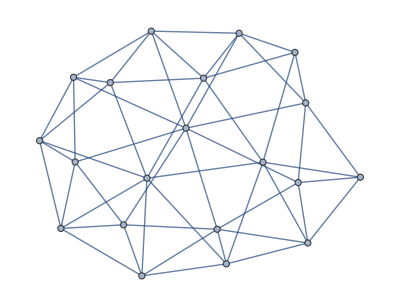
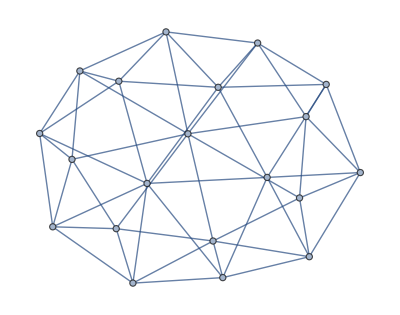
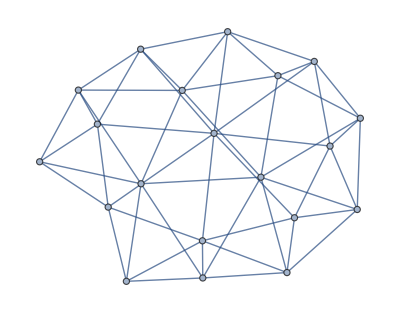
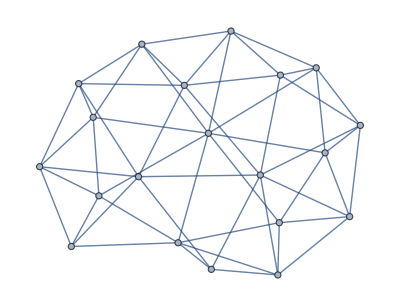
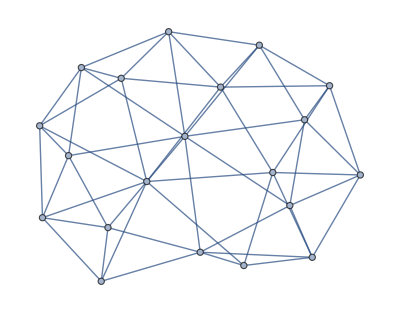
{{18,10,8,10},{18,10,8,10},{18,10,8,10},{18,10,8,10},{18,10,8,10},2421,{ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24-ChromaticPolynomial[-Graphics-,4]/24,10},{ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24-ChromaticPolynomial[-Graphics-,4]/24,10},{ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24-ChromaticPolynomial[-Graphics-,4]/24,10},{ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24,ChromaticPolynomial[-Graphics-,4]/24-ChromaticPolynomial[-Graphics-,4]/24,10}}
 |  |  |  |

```mathematica
gef3=Flatten[
ParallelTable[
PrintTemporary[k];
Calc[k],{k,1,50}],
1]
```

```mathematica
ChromaticPolynomial[-Graphics-,4]/24
```

ChromaticPolynomial[-Graphics-,4]/24

```mathematica
VerifyHypothesis23[value_]:=
{AllTrue[Map[With[
{rec=#},
rec[[3]]/4<=rec[[2]]<=rec[[3]]*4
]&,value],TrueQ]
,
AllTrue[Map[With[
{rec=#},
rec[[2]]/4<=rec[[3]]<=rec[[2]]*4
]&,value],TrueQ]
,
AllTrue[Map[With[
{rec=#},
rec[[2]]5/4<=rec[[1]]<=rec[[2]]*5
]&,value],TrueQ]
,
AllTrue[Map[With[
{rec=#},
rec[[3]]5/4<=rec[[1]]<=rec[[3]]*5
]&,value],TrueQ]
}
```

```mathematica
VerifyHypothesis23[gef3]
```

{False,False,False,False}

```mathematica
ExperimentBis[g_,edge_]:=Block[{},
With[
{e=ChromaticPolynomial[EdgeDelete[g,edge],x]//NullBaseCoeff,
t=ChromaticPolynomial[g,x]//NullBaseCoeff,
c=ChromaticPolynomial[EdgeContract[g,edge],x]//NullBaseCoeff},
Map[Map[First[Last[#]]&,#]&,FactorInteger[{e,t ,PadRight[c,Length[e]]}]]
]
]
```

```mathematica
Ratios
```

```mathematica
CalcBis[k_]:=With[
{g=Graph[plantri[[k]]]},
Table[TableForm[ExperimentBis[g,e],TableDepth->2],{e,Select[EdgeList[g],VertexDegree[g,#[[1]]]>5||VertexDegree[g,#[[2]]]&]}]
]
```

```mathematica
Clear[CalcBis]
```

```mathematica
Flatten[
Table[
PrintTemporary[k];
CalcBis[k],{k,2,3}],
1]//TableForm
```

0 | 95891 | 24907 | 4391 | 2417 | 34721 | 1102847 | 41 | 7457 | 105491 | 40933 | 2909 | 191 | 7 | 1
0 | 1061 | 3163 | 142223 | 4931497 | 1381 | 5077 | 154321 | 593 | 60457 | 277 | 31 | 101 | 3 | 1
0 | 593 | 156601 | 42727 | 619 | 99989 | 48989 | 70957 | 97 | 97 | 1193 | 23 | 11 | 1 | 0
0 | 95891 | 24907 | 4391 | 2417 | 34721 | 1102847 | 41 | 7457 | 105491 | 40933 | 2909 | 191 | 7 | 1
0 | 1061 | 3163 | 142223 | 4931497 | 1381 | 5077 | 154321 | 593 | 60457 | 277 | 31 | 101 | 3 | 1
0 | 593 | 156601 | 42727 | 619 | 99989 | 48989 | 70957 | 97 | 97 | 1193 | 23 | 11 | 1 | 0
0 | 95891 | 24907 | 4391 | 2417 | 34721 | 1102847 | 41 | 7457 | 105491 | 40933 | 2909 | 191 | 7 | 1
0 | 1061 | 3163 | 142223 | 4931497 | 1381 | 5077 | 154321 | 593 | 60457 | 277 | 31 | 101 | 3 | 1
0 | 593 | 156601 | 42727 | 619 | 99989 | 48989 | 70957 | 97 | 97 | 1193 | 23 | 11 | 1 | 0
0 | 95891 | 24907 | 4391 | 2417 | 34721 | 1102847 | 41 | 7457 | 105491 | 40933 | 2909 | 191 | 7 | 1
0 | 1061 | 3163 | 142223 | 4931497 | 1381 | 5077 | 154321 | 593 | 60457 | 277 | 31 | 101 | 3 | 1
0 | 593 | 156601 | 42727 | 619 | 99989 | 48989 | 70957 | 97 | 97 | 1193 | 23 | 11 | 1 | 0
0 | 95891 | 24907 | 4391 | 2417 | 34721 | 1102847 | 41 | 7457 | 105491 | 40933 | 2909 | 191 | 7 | 1
0 | 1061 | 3163 | 142223 | 4931497 | 1381 | 5077 | 154321 | 593 | 60457 | 277 | 31 | 101 | 3 | 1
0 | 593 | 156601 | 42727 | 619 | 99989 | 48989 | 70957 | 97 | 97 | 1193 | 23 | 11 | 1 | 0
0 | 95891 | 24907 | 4391 | 2417 | 34721 | 1102847 | 41 | 7457 | 105491 | 40933 | 2909 | 191 | 7 | 1
0 | 1061 | 3163 | 142223 | 4931497 | 1381 | 5077 | 154321 | 593 | 60457 | 277 | 31 | 101 | 3 | 1
0 | 593 | 156601 | 42727 | 619 | 99989 | 48989 | 70957 | 97 | 97 | 1193 | 23 | 11 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 24469 | 137633 | 6479021 | 8623 | 7109 | 1315907 | 35591 | 83 | 797 | 3607 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 359 | 1510493 | 1187689 | 14103127 | 542023 | 2131 | 2371 | 136727 | 1153 | 11411 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 24469 | 137633 | 6479021 | 8623 | 7109 | 1315907 | 35591 | 83 | 797 | 3607 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 359 | 1510493 | 1187689 | 14103127 | 542023 | 2131 | 2371 | 136727 | 1153 | 11411 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 24469 | 137633 | 6479021 | 8623 | 7109 | 1315907 | 35591 | 83 | 797 | 3607 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 359 | 1510493 | 1187689 | 14103127 | 542023 | 2131 | 2371 | 136727 | 1153 | 11411 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 24469 | 137633 | 6479021 | 8623 | 7109 | 1315907 | 35591 | 83 | 797 | 3607 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 359 | 1510493 | 1187689 | 14103127 | 542023 | 2131 | 2371 | 136727 | 1153 | 11411 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 115429 | 11003 | 919 | 1180237 | 22861 | 81901 | 22147 | 58979 | 55147 | 3989 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 6581 | 3533 | 2324183 | 1981997 | 7681 | 193811 | 480107 | 2237 | 6689 | 971 | 109 | 101 | 3 | 1 | 0
0 | 24469 | 137633 | 6479021 | 8623 | 7109 | 1315907 | 35591 | 83 | 797 | 3607 | 61 | 113 | 97 | 19 | 1
0 | 16363 | 95231 | 6343877 | 221059 | 342803 | 9871 | 353 | 3673 | 2707 | 661 | 2039 | 37 | 13 | 13 | 1
0 | 359 | 1510493 | 1187689 | 14103127 | 542023 | 2131 | 2371 | 136727 | 1153 | 11411 | 109 | 101 | 3 | 1 | 0

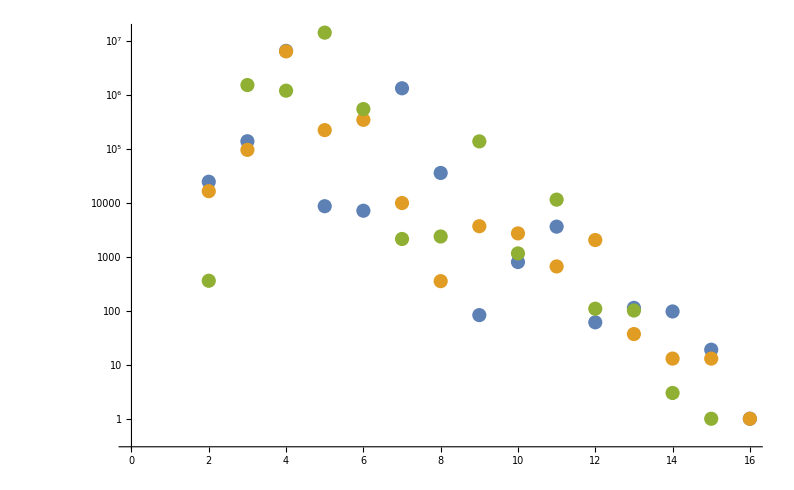

```mathematica
ListLogPlot[{{0, 24469, 137633, 6479021, 8623, 7109, 1315907, 35591, 83, 797, 3607, 61, 113, 97, 19, 1}, {0, 16363, 95231, 6343877, 221059, 342803, 9871, 353, 3673, 2707, 661, 2039, 37, 13, 13, 1}, {0, 359, 1510493, 1187689, 14103127, 542023, 2131, 2371, 136727, 1153, 11411, 109, 101, 3, 1, 0}}]
```

```mathematica
N[Log[1566010]]
```

14.264

```mathematica
156601^2
```

24523873201